### Notebook for computing EDL profiles on Mars caseyhandmer.com github.com/CHandmer

You are encouraged to use, modify, adapt, mercilessly torment, etc this code, but please be sure to give it full attribution whenever you publish.
This code is supplied as is and with no guarantee of functionality, support, predictive capacity, or any other useful attribute.

#### Mars physical parameters

This is a formula for the density of Mars’ atmosphere, with a scale height of 11.2km, somewhat larger than Earth’s. The gravity, at 3.71m/s^2, is, like everything else, in SI units.

```mathematica
ρ=0.02 Exp[-y[t]/11200];
gm=3.71;
```

#### The solution machinery

This function takes as arguments, respectively, [entry angle (degrees), seasonal atmospheric density multiplier, shield area, mass, drag coefficient, lift-to-drag coefficient, entry speed (m/s)]. As you will see below, this system is sufficiently versatile that you can plug, eg, functional dependence into the lift-to-drag variable. The equation solver simply solves ballistic motion in a variable density background. This is really hard to do by hand.

```mathematica
SolFunc[θd_,ρm_, A_, m0_, Cd_,Ld_,vE_]:=Catch[
θ=θd*π/180;startheight=140000.;minalt=0.;tc=0;
eqns={x''[t]==-0.5 ρm ρ Sqrt[x'[t]^2+y'[t]^2] A Cd (x'[t]+Ld  y'[t])/m0,y''[t]==-gm-0.5 ρm ρ Sqrt[x'[t]^2+y'[t]^2]A Cd (y'[t]-Ld  x'[t])/m0};
bcs={x[0]==0.,y[0]==startheight,x'[0]==vE Cos[θ], y'[0]==-vE Sin[θ]};
soltemp=NDSolve[Join[eqns,bcs],{y,x},{t,0,5000},Method->{"EventLocator","Event"->y[t],"EventAction":>Set[tc,t]},MaxSteps->1000000];
Throw[{tc,soltemp}]];
```

This function eats the same variables and throws out the usual entry profile graph. You’re welcome!

```mathematica
VelAltFunction[θd_,ρm_, A_, m0_, Cd_,Ld_,vE_]:=Catch[
sol=SolFunc[θd,ρm, A, m0, Cd,Ld,vE];
crashtime=sol[[1]];
sol=sol[[2]];
Throw[ParametricPlot[{Sqrt[x'[t]^2+y'[t]^2],y[t]}/.sol,{t,0,crashtime},PlotRange->{{0,1.1vE},{0,140000}},AspectRatio->0.6]]];
```

### Verification against historical data

These data taken from http://www .4frontiers.us/dev/assets/Braun_Paper_on _Mars _EDL.pdf (the MSL and Phoenix data is uncertain).

This data taken from wikimedia commons.

First, we’ll reproduce the above graph using this system. The inputs are as above, with names and colours added. 
[name, entry angle, atmosphere thickness (season), area, mass, drag coeff, lift/drag coeff, entry speed, colour]

```mathematica
legacydata={{"Viking",17,1,π(0.5*3.5)^2,992,992/(64 π(0.5*3.5)^2),0.18,4550(*4700*),Red},{"Pathfinder",14.06,1,π(0.5*2.65)^2,584,584/(63 π(0.5*2.65)^2),0,7260,Green},
{"MER",11.49,1,π(0.5*2.65)^2,829.5,829.5/(94π(0.5*2.65)^2),0,5550(*5450*),Blue},
{"Phoenix",12.5,1,π(0.5*2.65)^2,600,600/(70π(0.5*2.65)^2),0.06,5850(*5670*),Orange},
{"Curiosity",15.2,1,π(0.5*4.6)^2,2800,2800/(155π(0.5*4.6)^2),0.22,5700,Black}};
```

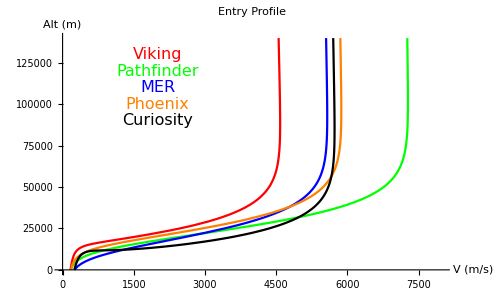

```mathematica
samporder={2,1,3,4,5};
figs=Table[Apply[VelAltFunction,legacydata[[i,2;;8]]],{i,samporder}];
Do[figs[[i,1,1,3,1,4]]=legacydata[[samporder[[i]],-1]];,{i,1,5}]
superimp=Show[figs,ImageSize->500,Epilog->Table[Inset[Style[legacydata[[i,1]],legacydata[[i,-1]],16],{2000,140000-10000i}],{i,1,Length[legacydata]}],AxesStyle->14,AxesLabel->{"V (m/s)","Alt (m)"},PlotLabel->Style["Entry Profile",Black,15]]
```

These profiles are reassuringly close to the historical data presented above.

#### Step into the unknown

For this section, we’re going to experiment with lifting bodies. They have an additional complication, which is that they tend to skip, producing a profile like this:

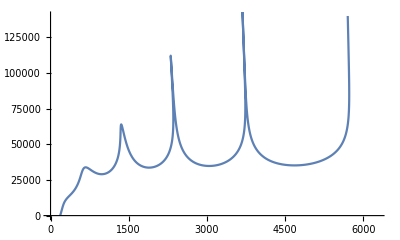

```mathematica
VelAltFunction[15.2,1,π(0.5*4.6)^2,2800,2800/(155π(0.5*4.6)^2),1.5,5700]
```

In practice, vehicles prone to skipping, including the Space Shuttle and the Apollo Command Module would bank their craft left and right to avoid climbing up out of the atmosphere. Including a control system in this simple model is overkill, all I do is introduce a sign function that zeros out the lift if the vehicle tries to climb faster than some rate (here, 50m/s). The same profile as above now looks much more reasonable.

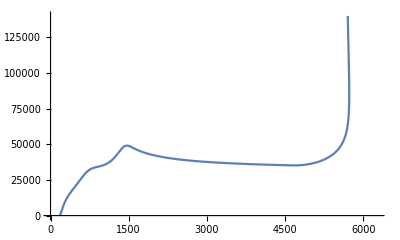

```mathematica
noclimb=0.5+0.5Tanh[-y'[t]+50];
VelAltFunction[15.2,1,π(0.5*4.6)^2,2800,2800/(155π(0.5*4.6)^2),1.5noclimb,5700]
```

While we’re doing individual test cases is a good time to get at a few other variables under the hood. This one plots acceleration as a function of velocity, instead of altitude. In ParametricPlot[]. one can change the two arguments to any function of t, x, x’, x’’, etc you may like.

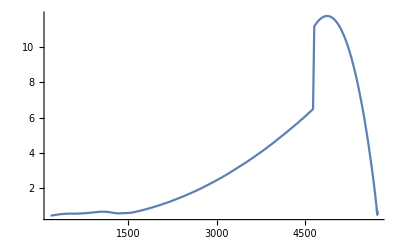

```mathematica
ParametricPlot[{Sqrt[x'[t]^2+y'[t]^2],(3.8+Sqrt[x''[t]^2+y''[t]^2])/9.8}/.sol,{t,0,crashtime},AspectRatio->0.6,PlotRange->All]
```

For the lifting body, winged vehicles I wanted to try, I used the Kuchemann approximation for supersonic L/D, with a variable constant discount to allow for aerodynamic inefficiency. The speed of sound on Mars is approximately 250m/s. Its reduction from Earth’s is primarily due to its lower temperature and higher mean molecular mass, than reduced density. https://en.wikipedia.org/wiki/Lift-to-drag_ratio#Supersonic.2Fhypersonic_lift_to_drag_ratios

```mathematica
kuchemann=4(Sqrt[x'[t]^2+y'[t]^2]/250+3)/(Sqrt[x'[t]^2+y'[t]^2]/250);
```

One can add more bells and whistles to this function. It is, for instance, possible to trigger a rocket landing below a certain speed, to evaluate fuel margins or whatever. .14

#### Let’s look at hypothetical vehicles

Here, I have some rough values tabulated for LDSD, the Mars Direct Hab, the Mars Direct Hab without the ADEPT umbrella shield, the SpaceX Red Dragon, the SpaceX Red Dragon with double the L/D ratio, the Space Shuttle, some generic triconic lifting body like the McDonnell Douglas AMaRV or the Constellation landers, and then three guesses for the SpaceX Mars Ship. I have included Curiosity for reference! As before, the column entries are for [name, entry angle, atmosphere thickness (season), area, mass, drag coeff, lift/drag coeff, entry speed, line color].

```mathematica
hypotheticalvehicledata={
{"Curiosity",15.2,1,π(0.5*4.6)^2,2800,2800/(155π(0.5*4.6)^2),0.22,5700,Black},
{"LDSD",12,1,π(0.5*6)^2,4000,1.6,0.18,5800,Blue},
{"MDHab",7,1,π*8^2,30000,1.6,0.18,6000,Red},
{"MDHabNoADEPT",7,1,π*4^2,30000,1.6,0.18,6000,Red},
{"RedDragon",15,1,π*1.8^2,7500,1.6,0.18,6000,Green},
{"RedDragonLift",15,1,π*1.8^2,7500,1.6,0.36,6000,Green},
{"SpaceShuttle",6,1,12*37,78000,1.5,0.2kuchemann noclimb,6000,Purple},
{"Triconic",8,1,11*40,180000,1.5,0.2 kuchemann noclimb,6000,Magenta},
{"MS1",5,1,12*49.5,800000,1.5,0.2 kuchemann noclimb,8500,Orange},
{"MS2",5,1,12*49.5,800000,1.5,0.15 kuchemann noclimb,8500,Orange},
{"MS3",5,1,12*49.5,800000,1.5,0.1 kuchemann noclimb,8500,Orange}};
```

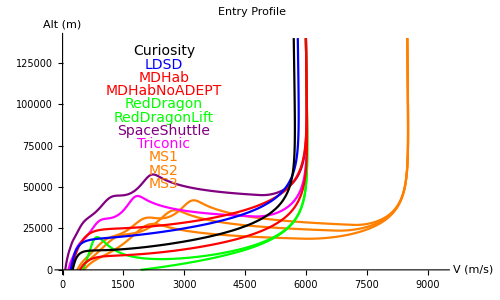

```mathematica
samporder=Table[i,{i,1,Length[hypotheticalvehicledata]}];
figs=Table[Apply[VelAltFunction,hypotheticalvehicledata[[i,2;;8]]],{i,samporder}];
Do[figs[[i,1,1,3,1,4]]=hypotheticalvehicledata[[samporder[[i]],-1]];,{i,1,Length[samporder]}]
Show[Reverse[figs],ImageSize->500,Epilog->Table[Inset[Style[hypotheticalvehicledata[[i,1]],hypotheticalvehicledata[[i,-1]],14],{2500,140000-8000i}],{i,1,Length[hypotheticalvehicledata]}],AxesStyle->14,AxesLabel->{"V (m/s)","Alt (m)"},PlotLabel->Style["Entry Profile",Black,15]]
```